My Little Mathematica Diary

This describes a simple, two-species molecular titration reaction. The output that we measure is C, produced by the activator.

```mathematica
rsys={
rxn[a+b,ab,1],
rxn[a,a+c,5],

conc[a,1],
conc[b,1]
};
```

This will generate the following dynamic behavior:

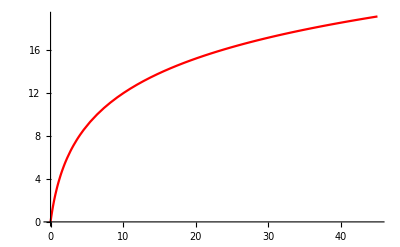

```mathematica
tmax=45;
sol=SimulateRxnsys[rsys,tmax];
plotter={c[t]}/.sol;
Plot[plotter,{t,0,tmax},PlotRange->All,PlotStyle->{{Red},{Green}}]
```

First we should verify that it is a simple enough model to play with (for now). To be more precise, let’s look at how sensitive it is to changes in input.

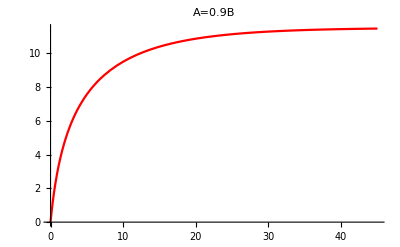

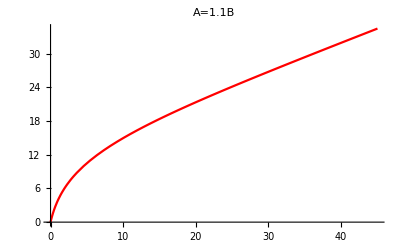

```mathematica
rsys={
rxn[a+b,ab,1],
rxn[a,a+c,5],

conc[a,0.9],
conc[b,1]
};

tmax=45;
sol=SimulateRxnsys[rsys,tmax];
plotter={c[t]}/.sol;
Plot[plotter,{t,0,tmax},PlotRange->All,PlotStyle->{{Red},{Green}},PlotLabel->"A=0.9B"]

rsys={
rxn[a+b,ab,1],
rxn[a,a+c,5],

conc[a,1.1],
conc[b,1]
};

tmax=45;
sol=SimulateRxnsys[rsys,tmax];
plotter={c[t]}/.sol;
Plot[plotter,{t,0,tmax},PlotRange->All,PlotStyle->{{Red},{Green}},PlotLabel->"A=1.1B"]
```

This seems OK with respect to the ultrasensitivity. We can worry about quantifying this ultrasensitivity later, and add additional components to generate steady states.

If we extend the simulation, the same log-growth behavior appears:

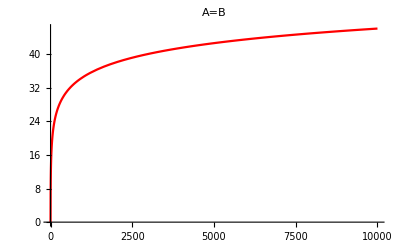

```mathematica
rsys={
rxn[a+b,ab,1],
rxn[a,a+c,5],

conc[a,1],
conc[b,1]
};

tmax=10000;
sol=SimulateRxnsys[rsys,tmax];
plotter={c[t]}/.sol;
Plot[plotter,{t,0,tmax},PlotRange->All,PlotStyle->{{Red},{Green}},PlotLabel->"A=B"]
```

Let’s also see what happens when we change some other parameters.

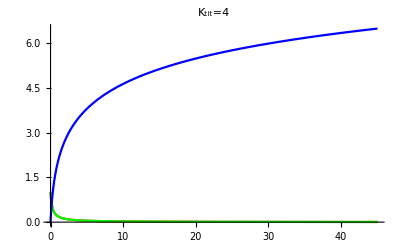

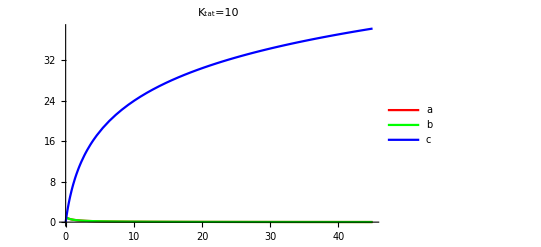

```mathematica
rsys={
rxn[a+b,ab,4],
rxn[a,a+c,5],

conc[a,1],
conc[b,1]
};

tmax=45;
sol=SimulateRxnsys[rsys,tmax];
plotter={a[t],b[t],c[t]}/.sol;
Plot[plotter,{t,0,tmax},PlotRange->All,PlotStyle->{{Red},{Green}, Blue},PlotLabel->"K_tit=4"]

rsys={
rxn[a+b,ab,1],
rxn[a,a+c,10],

conc[a,1],
conc[b,1]
};

tmax=45;
sol=SimulateRxnsys[rsys,tmax];
plotter={a[t],b[t],c[t]}/.sol;
Plot[plotter,{t,0,tmax},PlotRange->All,PlotStyle->{{Red},{Green},{Blue}},PlotLabel->"K_tat=10",PlotLegends->{"a","b","c"}]
```

As expected, the output (C) increases when increasing the K_tat, and decreases when increasing K_tat. 
The second plot highlights a feature that was similar to the case when we extended the duration fo the simulation - .7f C just continues to increase, even after A should be have been mostly depleted! I interpret it a one of two reasons:
	1. It’s a result of the underlying mechanisms on how the CRNSimulator package is implemented. Though, I’d agree that this seems unlikely.
	2. The concentration of A never completely depletes.  It will asymptotically approach zero, but the few A “molecules” in the simulation will still bind to C with higher affinity than to B. In retrospect, this makes a lot of sense - the growth of C looks logarithmic; because A continually decreases, it effectively becomes “harder” over time to find an A in solution.

As noted in an earlier plot, we can achieve pretty good steady state if A is 90% of B. Can we get the proportion any closer to 1?

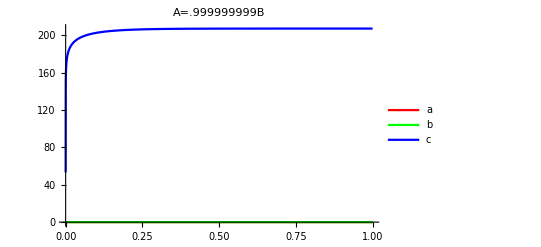

```mathematica
rsys={
rxn[a+b,ab,1],
rxn[a,a+c,10],

conc[a,.999999999],
conc[b,1]
};

tmax=10000000000;
sol=SimulateRxnsys[rsys,tmax];
plotter={a[t],b[t],c[t]}/.sol;
Plot[plotter,{t,0,tmax},PlotRange->All,PlotStyle->{{Red},{Green},{Blue}},PlotLabel->"A=.999999999B",PlotLegends->{"a","b","c"}]

rsys={
rxn[a+b,ab,1],
rxn[a,a+c,10],

conc[a,1],
conc[b,1]
};
(*
tmax=1000000000000000;
sol=SimulateRxnsys[rsys,tmax];
plotter={a[t],b[t],c[t]}/.sol;
Plot[plotter,{t,0,tmax},PlotRange->All,PlotStyle->{{Red},{Green},{Blue}},PlotLabel->"A=.999999999B",PlotLegends->{"a","b","c"}]
*)
```

It seems like you can get arbitrarily close to a 1:1 ratio between A and B, and with long enough time, eventually reach steady state.

```mathematica
ϵ=0.001;
f[time_,ratio_]:=Module[{plotter,sol,test,rng,y,res,rsys,step},
rsys={
rxn[a+b,ab,1],
rxn[a,a+c,10],

conc[a,ratio],
conc[b,1]
};
sol=SimulateRxnsys[rsys,time];
plotter={c[t]}/.sol;
fn=plotter[[1]][[0]];
rng = Range[1,time,time/100]; (* 1000 data points *)
y=Table[fn[i*time/100],{i,Length[rng]}];
res=Thread[{rng,y}];
i=1;
While[(res[[i+1,2]]-res[[i,2]])/(res[[i,2]])>=ϵ,i=i+1];
Return[res[[i,1]]]
]


N[f[100,0.9]]
```

37.

100

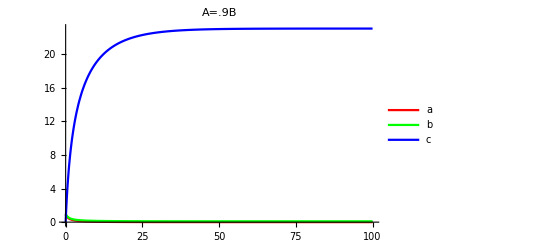

```mathematica
rsys={
rxn[a+b,ab,1],
rxn[a,a+c,10],

conc[a,0.9],
conc[b,1]
};

tmax=100
sol=SimulateRxnsys[rsys,tmax];
plotter={a[t],b[t],c[t]}/.sol;
Plot[plotter,{t,0,tmax},PlotRange->All,PlotStyle->{{Red},{Green},{Blue}},PlotLabel->"A=.9B",PlotLegends->{"a","b","c"}]
```

Other things that I explored this week:
- learning about modules and functions

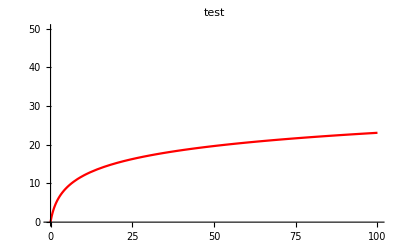

```mathematica
basicTitration1[ktit_,ktat_,concA_,concB_,tmax_:45,title_]:= 
Module[{a,b,c,ab,sol,plotter,rsys},
rsys={
rxn[a+b,ab,ktit],
rxn[a,a+c,ktat],

conc[a,concA],
conc[b,concB]
};
sol=SimulateRxnsys[rsys,tmax];
plotter={c[t]}/.sol;
Plot[plotter,{t,0,tmax},PlotRange->{{0,tmax},{0,50}},PlotStyle->{{Red},{Green}},PlotLabel->title] 
]
basicTitration1[1,5,1,1,100,"test"]
```

```mathematica
Manipulate[basicTitration1[1,5,a,1,100,"C"],{{a,1,"A/B"},0.9,1,0.001}]
```